#### The dispersion relation function

```mathematica
Ene[kx_,ky_,a_,t1_,t2_]:=2{t1 Cos[kx a]+t2 Cos[ky a],t2 Cos[kx a]+t1 Cos[ky a],t2 Cos[kx a]+t2 Cos[ky a]};
```

#### choose a=1, t1=-1, t2=-0.2

```mathematica
F[a_,b_]:=Ene[a,b,1,-1,-0.2];
```

```mathematica
Plot3D[F[x,y],{x,-Pi/1,Pi/1},{y,-Pi/1,Pi/1},AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

#### Plot along Γ---M----X----Γ path

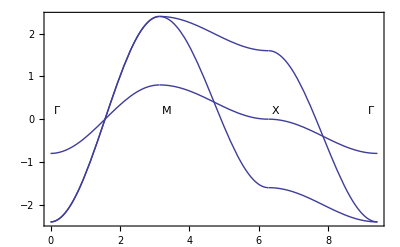

```mathematica
Plot[Piecewise[{{F[t,t],t≥0&&t<Pi},{F[Pi,-t+2Pi],t≥Pi&&t<2Pi},{F[Pi-t+2Pi,0],t≥2Pi&&t≤3Pi}}],{t,0,3Pi},Frame->True,GridLines->{{{Pi,Dashed},{2Pi,Dashed},{0,Dashed},{3Pi,Dashed}},{}},Epilog->{Inset["Γ",{0.2,0.2}],Inset["M",{Pi+0.2,0.2}],Inset["X",{2Pi+0.2,0.2}],Inset["Γ",{3Pi-0.2,0.2}]}]
```

#### Use manipulate to checke how how plot change with t2/t1

```mathematica
Manipulate[{F[a_,b_]:=Ene[a,b,1,-1,t2];Plot[Piecewise[{{F[t,t],t≥0&&t<Pi},{F[Pi,-t+2Pi],t≥Pi&&t<2Pi},{F[Pi-t+2Pi,0],t≥2Pi&&t≤3Pi}}],{t,0,3Pi},Frame->True,GridLines->{{{Pi,Dashed},{2Pi,Dashed},{0,Dashed},{3Pi,Dashed}},{}},Epilog->{Inset["Γ",{0.2,0.2}],Inset["M",{Pi+0.2,0.2}],Inset["X",{2Pi+0.2,0.2}],Inset["Γ",{3Pi-0.2,0.2}]},ImageSize->Scaled[1]]},{t2,-2,2}]
```

#### Define angular momentum matrix and spin matrix

```mathematica
LX=({{0, 0, 0}, {0, 0, -I}, {0, I, 0}})
LY=({{0, 0, I}, {0, 0, 0}, {-I, 0, 0}})

SZ=({{1/2, 0}, {0, -1/2}})
```

{{0,0,0},{0,0,-ⅈ},{0,ⅈ,0}}

{{0,0,ⅈ},{0,0,0},{-ⅈ,0,0}}

{{1/2,0},{0,-1/2}}

```mathematica
LZ=({{0, -I, 0}, {I, 0, 0}, {0, 0, 0}})
```

{{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}}

```mathematica
SX=({{0, 1/2}, {1/2, 0}})
```

{{0,1/2},{1/2,0}}

```mathematica
SY=({{0, -I/2}, {I/2, 0}})
```

{{0,-ⅈ/2},{ⅈ/2,0}}

#### Define the spin-orbital hamiltonian

```mathematica
Hsoc=KroneckerProduct[LX,SX]+KroneckerProduct[LY,SY]+KroneckerProduct[LZ,SZ];
```

```mathematica
MatrixForm[Hsoc]
```

(0 | 0 | -ⅈ/2 | 0 | 0 | 1/2
0 | 0 | 0 | ⅈ/2 | -1/2 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | -1/2 | 0 | ⅈ/2 | 0 | 0
1/2 | 0 | ⅈ/2 | 0 | 0 | 0)

```mathematica
HH[t1_,t2_,λ_,kx_,ky_,a_]:=2({{t1 Cos[kx a]+t2 Cos[ky a], 0, 0, 0, 0, 0}, {0, t1 Cos[kx a]+t2 Cos[ky a], 0, 0, 0, 0}, {0, 0, t2 Cos[kx a]+t1 Cos[ky a], 0, 0, 0}, {0, 0, 0, t2 Cos[kx a]+t1 Cos[ky a], 0, 0}, {0, 0, 0, 0, t2 Cos[kx a]+t2 Cos[ky a], 0}, {0, 0, 0, 0, 0, t2 Cos[kx a]+t2 Cos[ky a]}})+λ Hsoc;
```

#### Plot band structure with spin-orbital coumpling

```mathematica
Manipulate[FF[kx_,ky_]:=Sort[Eigenvalues[HH[-1,-0.2,λ,kx,ky,1]]];Plot[Piecewise[{{FF[t,t],t≥0&&t<Pi},{FF[Pi,-t+2Pi],t≥Pi&&t<2Pi},{FF[Pi-t+2Pi,0],t≥2Pi&&t≤3Pi}}],{t,0,3Pi},Frame->True,GridLines->{{{Pi,Dashed},{2Pi,Dashed},{0,Dashed},{3Pi,Dashed}},{}},Epilog->{Inset["Γ",{0.2,0.2}],Inset["M",{Pi+0.2,0.2}],Inset["X",{2Pi+0.2,0.2}],Inset["Γ",{3Pi-0.2,0.2}]}],{λ,-10,10}]
```